{{α[t]→InterpolatingFunction[…][t],β[t]→InterpolatingFunction[…][t],γ[t]→InterpolatingFunction[…][t]}}

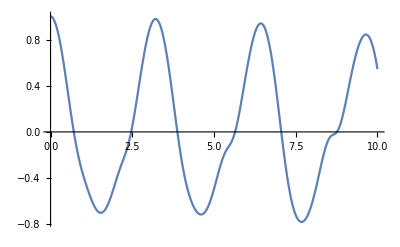

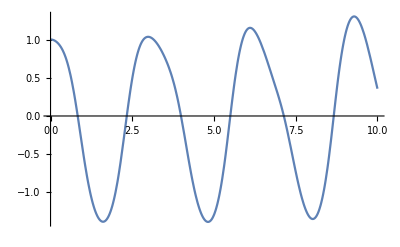

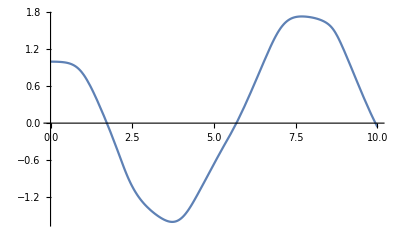

```mathematica
eqns={
α''[t] Subscript[J, OC]+1/2 (2 α'[t] γ'[t] Sin[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]+2 α'[t] β'[t] Sin[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC])+g Sin[α[t]] Subscript[l, OC] Subscript[m, BA]+1/2 (2 γ''[t] Cos[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]-2 (α'[t]-γ'[t]) γ'[t] Sin[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]+2 β''[t] Cos[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC]-2 (α'[t]-β'[t]) β'[t] Sin[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC]+2 α''[t] Subscript[l, OC]^2 Subscript[m, BA])+g Sin[α[t]] Subscript[l, OC] Subscript[m, CB]+α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Cos[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC]-2 (α'[t]-β'[t]) β'[t] Sin[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC]+2 α''[t] Subscript[l, OC]^2) Subscript[m, CB]+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]==0,
1/2 (2 β'[t] γ'[t] Sin[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]-2 α'[t] β'[t] Sin[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC])+g Sin[β[t]] Subscript[l, CB] Subscript[m, BA]+1/2 (2 γ''[t] Cos[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]-2 (β'[t]-γ'[t]) γ'[t] Sin[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]+2 α''[t] Cos[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC]-2 α'[t] (α'[t]-β'[t]) Sin[α[t]-β[t]] Subscript[l, CB] Subscript[l, OC]+2 β''[t] Subscript[l, CB]^2 Subscript[m, BA])+g Sin[β[t]] Subscript[k, CB] Subscript[m, CB]-α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Subscript[J, CB]+2 α''[t] Cos[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB]-2 α'[t] (α'[t]-β'[t]) Sin[α[t]-β[t]] Subscript[k, CB] Subscript[l, OC] Subscript[m, CB])==0,
-β'[t] γ'[t] Sin[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]-α'[t] γ'[t] Sin[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]+1/2 (2 γ''[t] Subscript[J, BA]+2 (β''[t] Cos[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]-β'[t] (β'[t]-γ'[t]) Sin[β[t]-γ[t]] Subscript[k, BA] Subscript[l, CB]+α''[t] Cos[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]-α'[t] (α'[t]-γ'[t]) Sin[α[t]-γ[t]] Subscript[k, BA] Subscript[l, OC]))+g Sin[γ[t]] Subscript[k, BA] Subscript[m, BA]==0,

α[0]==1,β[0]==1,γ[0]==1,α'[0]==0,β'[0]==0,γ'[0]==0

};

g=9.81;
Subscript[m, BA]=1;
Subscript[m, CB]=1;
Subscript[m, OC]=1;
Subscript[J, BA]=1.01;
Subscript[J, CB]=1.25;
Subscript[J, OC]=1.25;
Subscript[l, BA]=0.2;
Subscript[l, CB]=1;
Subscript[l, OC]=1;
Subscript[k, BA]=0.1;
Subscript[k, CB]=0.5;
Subscript[k, OC]=0.5;
u=0;
q=0;
h=0;

sol = NDSolve[eqns,{α[t],β[t],γ[t]},{t,0,20} ]
Plot[Evaluate[α[t]/.sol],{t,0,10},PlotRange->All]
Plot[Evaluate[β[t]/.sol],{t,0,10},PlotRange->All]
Plot[Evaluate[γ[t]/.sol],{t,0,10},PlotRange->All]
```